```mathematica
(*Define relevant functions*)
chiSpecial1[psi_, zetasq_] := -(1/2) *(((psi*zetasq - zetasq -1)^2 + 4 * zetasq * psi)^(1/2) + (psi*zetasq -
zetasq -1)) / zetasq;
d0Special1[zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
chival^5*zetasq^3 - 3*chival^4*zetasq^2-(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3 + 2*chival^3*zetasq^2 + 3*chival^3*zetasq -(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2 - 2*chival^2*zetasq - chival^2 - 3*psi1*psi2*chival*zetasq + psi1*psi2];
d0Special1mod[zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival= chi;
chival^5*zetasq^3 - 3*chival^4*zetasq^2-(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3 + 2*chival^3*zetasq^2 + 3*chival^3*zetasq -(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2 - 2*chival^2*zetasq - chival^2 - 3*psi1*psi2*chival*zetasq + psi1*psi2];

d1Special1[zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];chival^6*zetasq^3 - 2*chival^5*zetasq^2-(psi1*psi2-psi1-psi2+1)*chival^4*zetasq^3 + chival^4*zetasq^2 + chival^4*zetasq -2*(1-(psi1 * psi2))*chival^3*zetasq^2 -(psi1 + psi2 + psi1*psi2 + 1)*chival^2*zetasq  - chival^2];

d1Special1mod[zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival=chi;chival^6*zetasq^3 - 2*chival^5*zetasq^2-(psi1*psi2-psi1-psi2+1)*chival^4*zetasq^3 + chival^4*zetasq^2 + chival^4*zetasq -2*(1-(psi1 * psi2))*chival^3*zetasq^2 -(psi1 + psi2 + psi1*psi2 + 1)*chival^2*zetasq  - chival^2];

d2Special1 [zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
-(psi1-1)*chival^3 * zetasq^2 - chival^3 * zetasq + (psi1+1)*chival^2*zetasq + chival^2];
d2Special1mod [zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival=chi;
-(psi1-1)*chival^3 * zetasq^2 - chival^3 * zetasq + (psi1+1)*chival^2*zetasq + chival^2];

SSpecial1[F1_, Fs_, tau_,psi1_,psi2_,zetasq_]:=
Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
F1^2 *(zetasq)*(d1Special1[zetasq,psi1,psi2]/((chival *(zetasq) -1 )*d0Special1[zetasq,psi1,psi2]))+ (tau^2+Fs^2)*(zetasq)* (d2Special1[zetasq,psi1,psi2]/d0Special1[zetasq,psi1,psi2])];
SSpecialmod[F1_, Fs_, tau_,psi1_,psi2_,zetasq_, chi_]:=
F1^2 *(zetasq)*(d1Special1mod[zetasq,psi1,psi2, chi]/((chi *(zetasq) -1 )*d0Special1mod[zetasq,psi1,psi2, chi]))+ (tau^2+Fs^2)*(zetasq)* (d2Special1mod[zetasq,psi1,psi2, chi]/d0Special1mod[zetasq,psi1,psi2, chi]);
chiSpecial1[psi_, zetasq_] := -(1/2) *(((psi*zetasq - zetasq -1)^2 + 4 * zetasq * psi)^(1/2) + (psi*zetasq -
zetasq -1)) / zetasq;
eps0[zetasq_, psi1_, psi2_] :=Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];
-chival^5*zetasq^3+3*chival^4*zetasq^2+(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3-2*chival^3*zetasq^2-3*chival^3*zetasq+(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2+2*chival^2*zetasq+chival^2+3*psi1*psi2*chival*zetasq-psi1*psi2];
eps0mod[zetasq_, psi1_, psi2_, chi_] :=Module[{chival}, chival = chi;
-chival^5*zetasq^3+3*chival^4*zetasq^2+(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3-2*chival^3*zetasq^2-3*chival^3*zetasq+(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2+2*chival^2*zetasq+chival^2+3*psi1*psi2*chival*zetasq-psi1*psi2];

eps1[zetasq_, psi1_, psi2_] := Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];
psi2*chival^3*zetasq^2-psi2*(chival^2)*zetasq+psi1*psi2*chival*zetasq-psi1*psi2];
eps1mod[zetasq_, psi1_, psi2_, chi_] := Module[{chival}, chival = chi;
psi2*chival^3*zetasq^2-psi2*(chival^2)*zetasq+psi1*psi2*chival*zetasq-psi1*psi2];

eps2[zetasq_, psi1_, psi2_] := Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];chival^5*zetasq^3-3*chival^4*zetasq^2+(psi1-1)*chival^3*zetasq^3+2*chival^3*zetasq^2+3*chival^3*zetasq+(-psi1-1)*(chival^2)*(zetasq^2)-2*(chival^2)*zetasq-(chival^2)];
eps2mod[zetasq_, psi1_, psi2_, chi_] := Module[{chival}, chival = chi;
chival^5*zetasq^3-3*chival^4*zetasq^2+(psi1-1)*chival^3*zetasq^3+2*chival^3*zetasq^2+3*chival^3*zetasq+(-psi1-1)*(chival^2)*(zetasq^2)-2*(chival^2)*zetasq-(chival^2)];

B[zetasq_, psi1_, psi2_] := eps1[zetasq, psi1, psi2] /eps0[zetasq, psi1, psi2];
Bmod[zetasq_, psi1_, psi2_, chi_] := eps1mod[zetasq, psi1, psi2, chi] /eps0mod[zetasq, psi1, psi2, chi];
V[zetasq_, psi1_, psi2_] := eps2[zetasq, psi1, psi2] /eps0[zetasq, psi1, psi2];
Vmod[zetasq_, psi1_, psi2_, chi_] := eps2mod[zetasq, psi1, psi2, chi] /eps0mod[zetasq, psi1, psi2, chi];
R[F1_,Fs_,tau_,psi1_,psi2_,zetasq_] := F1^2*B[zetasq,psi1,psi2]+(Fs^2+tau^2)*V[zetasq,psi1,psi2]+Fs^2;
Rmod[F1_,Fs_,tau_,psi1_,psi2_,zetasq_, chi_] := F1^2*Bmod[zetasq,psi1,psi2, chi]+(Fs^2+tau^2)*Vmod[zetasq,psi1,psi2, chi]+Fs^2;
```

```mathematica
alpha = 0.5;
F1=1;
Fs=Sqrt[0.5];
psi2=3;
tau=0;
zetasq = 2;
```

```mathematica
chiSpecial1[3.0, 2.7519316165878034]
```

-2.14487

```mathematica
g1 = Plot[Rmod[F1,Fs,tau,x*psi2,psi2,zetasq, chiSpecial1[Min[x*psi2, psi2], zetasq]], {x, 0, 5}];
```

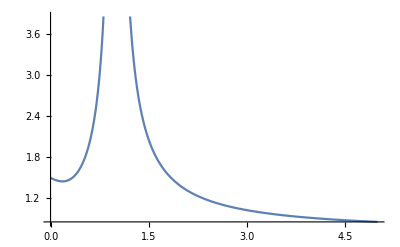

```mathematica
Show[g1]
```

```mathematica
g2 = Plot[Rmod[F1,Fs,tau,x*psi2,psi2,zetasq, chiSpecial1[Min[x*psi2, psi2], zetasq]], {x, 0, 5}];
```

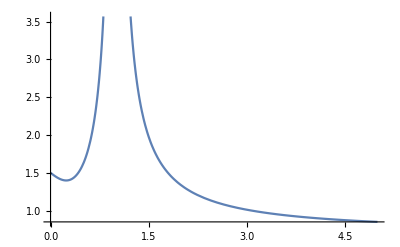

```mathematica
Show[g2]
```

```mathematica
g3 = Plot[SSpecialmod[F1, Fs, tau,x*psi2,psi2,zetasq,  chiSpecial1[Min[x*psi2, psi2], zetasq]], {x, 0, 5}];
```

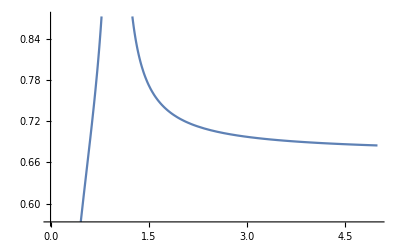

```mathematica
Show[g3]
```

```mathematica
g4 = Plot[0.5 * SSpecialmod[F1, Fs, tau,x*psi2,psi2,zetasq,  chiSpecial1[Min[x*psi2, psi2], zetasq]] + 0.5 *Rmod[F1,Fs,tau,x*psi2,psi2,zetasq, chiSpecial1[Min[x*psi2, psi2], zetasq]] , {x, 0, 5}];
```

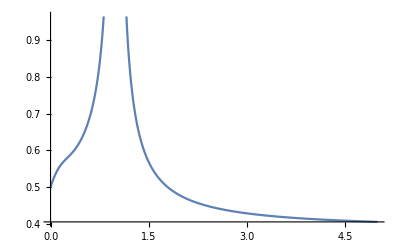

```mathematica
Show[g4]
```

```mathematica
SSpecialmod[F1,Fs,tau,psi1,psi2,2.7519316165878034, chiSpecial1[3.0, 2.7519316165878034]]
```

0.748329

```mathematica
(*Find zetasq as a function of chi*)
Solve[chi==chiSpecial1[psi, zetasq],zetasq]
```

{{zetasq→(chi+psi)/(chi (-1+chi+psi))}}

```mathematica
(*In the paper we identify x by chi. Find max and min of x*)
FullSimplify[Maximize[{chiSpecial1[psi, zetasq],zetasq≥0},zetasq],Assumptions->psi>0]
FullSimplify[Minimize[{chiSpecial1[psi, zetasq],zetasq≥0},zetasq],Assumptions->psi>0]
```

{Piecewise[{{1-psi, psi>1}, {0, True}}],{zetasq→Indeterminate}}

{-psi,{zetasq→Indeterminate}}

```mathematica
(*CASE 1 WHEN psi1 < psi2*)
(*Define our objective function for when psi1 < psi2*)
objective=((α)SSpecialmod[F1,Fs,tau, psi1,psi2,zetasq,chi]+(1-α)*Rmod[F1,Fs,tau,psi1, psi2,zetasq,chi]/.{zetasq->(chi+psi1)/(chi (-1+chi+psi1))})//FullSimplify;
(*Check that the objective is a decreasing line when alpha = 0*)
D[objective/.{α->0},chi]//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Compute second derivative with respect to chi MINUS basedline function. This is Otilde in the paper*)
secondDerMinusBaseline=D[objective,{chi,2}]-(2 F1^2 α)/(psi1-psi2)//Together//FullSimplify
```

-(2 F1^2 psi1 (-2 chi^3-3 chi^2 (-1+psi1)+(-1+psi1)^2 psi1) α)/((-psi1+(chi+psi1)^2)^3)

```mathematica
(*Show that secondDerMinusBaseline is always convex*)
(*We will assume without loss of generality that F1 = alpha = 1*)
(*First observe that the second derivative of Otilde is a rational function of x*)
secondDerOfsecondDerMinusBaseline=D[secondDerMinusBaseline/.{F1->1,α->1},{chi,2}]//Together//FullSimplify;
num=Numerator[secondDerOfsecondDerMinusBaseline]//FullSimplify;
den=Denominator[secondDerOfsecondDerMinusBaseline]//FullSimplify;
(*We show that both the numerator and denominator of the second derivative are non-positive*)
Maximize[{den,chi≥-psi1&&chi≤0&&chi≤1-psi1&&psi1>0&&psi1≠1},{chi,psi1}]
Maximize[{num,chi≥-psi1&&chi≤0&&chi≤1-psi1&&psi1>0&&psi1≠1},{chi,psi1}]
(*With a bit more of effort on can see that since psi1 neq 1 the denominator is actually strictly negative*)
Solve[den==0,chi]//FullSimplify
(*chi =-√psi1-psi1 is cearly outside the bounds for chi (note chi = x).*)
(*√psi1-psi1 is only inside [xL,xR] if psi1==1 since psi1>0*)
Minimize[{√psi1-psi1-Min[0,1-psi1],psi1>0},psi1]
```

Maximize::wksol: Warning: there is no maximum in the region in which the objective function is defined and the constraints are satisfied; a result on the boundary will be returned.

{0,{chi→0,psi1→0}}

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{0,{chi→Indeterminate,psi1→0}}

{{chi→-√psi1-psi1},{chi→-√psi1-psi1},{chi→-√psi1-psi1},{chi→-√psi1-psi1},{chi→-√psi1-psi1},{chi→√psi1-psi1},{chi→√psi1-psi1},{chi→√psi1-psi1},{chi→√psi1-psi1},{chi→√psi1-psi1}}

{0,{psi1→1}}

```mathematica
(*Compute the left end points of secondDerMinusBaseline and also for A1*)
(*This value is the y-coordinate of the A1 mentioned in the proof after it is divided by F^2_1 alpha*)
OtildexL=secondDerMinusBaseline/.{F1->1,α->1,chi->-psi1}//FullSimplify
```

2+2/psi1

```mathematica
(*Compute the right end points of secondDerMinusBaseline abd also for A3*)
(*This value is the y-coordinate of the A3 mentioned in the proof when psi1 < 1 after it is divided by F^2_1 alpha*)
OtildexR1=secondDerMinusBaseline/.{F1->1,α->1,chi->0}//FullSimplify
(*This value is the y-coordinate of the A3 mentioned in the proof when psi > 1 after it is divided by F^2_1 alpha*)
OtildexR2=secondDerMinusBaseline/.{F1->1,α->1,chi->1-psi1}//FullSimplify
```

2/(psi1-psi1^2)

(2 psi1)/(-1+psi1)

```mathematica
(*Show that the left most value of secondDerMinusBaseline is always smaller than the right most value of secondDerMinusBaseline*)
Minimize[{Max[OtildexR1,OtildexR2]-OtildexL,psi1>0},psi1]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{0,{psi1→0}}

```mathematica
(*show that left side is decreasing given that F1>0, psi1>0 and alpha >0*)
```

```mathematica
D[secondDerMinusBaseline, chi]/.{chi->-psi1}//FullSimplify
```

-(12 F1^2 α)/psi1

```mathematica
(*Calculation of A1*)
(*See above*)
```

```mathematica
(*Calculation of y-coordinate of A2 after we divide it by F^2_1 alpha*)
Minimize[{secondDerMinusBaseline/.{α->1,F1->1},chi≥-psi1&&chi≤0&&chi≤1-psi1&&psi1≥0},chi]//FullSimplify
```

{Piecewise[{{-1/2+(1+√(1-psi1))/psi1, 0<psi1≤1}, {1+√((-1+psi1)/psi1)-1/(2 psi1), psi1>1}, {∞, True}}],{chi→Piecewise[{{Root[5 psi1^2-2 √(-1+psi1) psi1^(5/2)-13 psi1^3+6 √(-1+psi1) psi1^(7/2)+13 psi1^4-6 √(-1+psi1) psi1^(9/2)-7 psi1^5+2 √(-1+psi1) psi1^(11/2)+2 psi1^6+(-6 psi1^2+12 √(-1+psi1) psi1^(5/2)+24 psi1^3-24 √(-1+psi1) psi1^(7/2)-30 psi1^4+12 √(-1+psi1) psi1^(9/2)+12 psi1^5) #1+(9 psi1+6 √(-1+psi1) psi1^(3/2)+12 psi1^2-36 √(-1+psi1) psi1^(5/2)-51 psi1^3+30 √(-1+psi1) psi1^(7/2)+30 psi1^4) #1^2+(4 psi1-24 √(-1+psi1) psi1^(3/2)-44 psi1^2+40 √(-1+psi1) psi1^(5/2)+40 psi1^3) #1^3+(3-21 psi1+30 √(-1+psi1) psi1^(3/2)+30 psi1^2-6 √((-1+psi1) psi1)) #1^4+(-6+12 psi1+12 √((-1+psi1) psi1)) #1^5+(2+2 √((-1+psi1)/psi1)-1/psi1) #1^6&,1], psi1>1}, {Root[2 psi1^2-2 √(1-psi1) psi1^2-psi1^3+6 √(1-psi1) psi1^3-5 psi1^4-6 √(1-psi1) psi1^4+5 psi1^5+2 √(1-psi1) psi1^5-psi1^6+(12 psi1^2+12 √(1-psi1) psi1^2-30 psi1^3-24 √(1-psi1) psi1^3+24 psi1^4+12 √(1-psi1) psi1^4-6 psi1^5) #1+(18 psi1+6 √(1-psi1) psi1-51 psi1^2-36 √(1-psi1) psi1^2+48 psi1^3+30 √(1-psi1) psi1^3-15 psi1^4) #1^2+(-32 psi1-24 √(1-psi1) psi1+52 psi1^2+40 √(1-psi1) psi1^2-20 psi1^3) #1^3+(-6-6 √(1-psi1)+33 psi1+30 √(1-psi1) psi1-15 psi1^2) #1^4+(12+12 √(1-psi1)-6 psi1) #1^5+(-1+2/psi1+(2 √(1-psi1))/psi1) #1^6&,1], 0<psi1<1}, {Indeterminate, True}}]}}

```mathematica
(*Calculation of A3*)
(*See above *)
```

```mathematica
(*calculation of beta_1*)
(*Case when psi1 ≤1*)
Solve[-1/2+(1+√(1-psi1))/psi1==-2/(psi1-psi2),psi2]//FullSimplify
(*Case when psi1 >=1*)
Solve[1+√((-1+psi1)/psi1)-1/(2 psi1)==-2/(psi1-psi2),psi2]//FullSimplify
```

{{psi2→(8-8 √(1-psi1)+(-4+psi1) psi1)/psi1}}

{{psi2→psi1 (-3-8 √(-1+psi1) √psi1+8 psi1)}}

```mathematica
(*calculation of beta_2*)
Solve[2+2/psi1==-2/(psi1-psi2),psi2]//FullSimplify
```

{{psi2→(psi1 (2+psi1))/(1+psi1)}}

```mathematica
(*calculation of beta_3*)
(*Case when psi1 ≤ 1*)
Solve[2/(psi1-psi1^2)==-2/(psi1-psi2),psi2]//FullSimplify
(*Case when psi1 >= 1*)
Solve[(2 psi1)/(-1+psi1)==-2/(psi1-psi2),psi2]//FullSimplify
```

{{psi2→-(-2+psi1) psi1}}

{{psi2→1-1/psi1+psi1}}

```mathematica
(*Compute the poly for critical points of the objective when psi1 neq 1*)
derObj=D[objective,chi]//Together//FullSimplify;
```

```mathematica
(*Get numerator of the above polynomial*)
num=Numerator[derObj]//FullSimplify;
```

```mathematica
(*Compute coefficients for poly when psi1 neq 1*)
((CoefficientList[num,chi]/.{F1^2->ρ*(Fs^2+tau^2)})/(Fs^2+tau^2))//FullSimplify
```

{(-1+psi1)^2 psi1^2 (psi2 ρ+α (-1+(-1+4 psi1-3 psi2) ρ)),2 (-1+psi1) psi1 (9 psi1^2 α ρ+psi2 α ρ-2 psi1 (α-psi2 ρ+(2+3 psi2) α ρ)),2 psi1 ((-1+3 psi1) psi2 ρ+α (1-3 psi1+ρ+psi1 (-12+16 psi1-9 psi2) ρ+4 psi2 ρ)),4 psi1 (psi2 ρ+α (-1+(-2+7 psi1-3 psi2) ρ)),psi2 ρ+α (-1+(-1+12 psi1-3 psi2) ρ),2 α ρ}

```mathematica
(*get expression for the denominator*)
den=Denominator[derObj]//FullSimplify
(*check that the roots of the denominator do not make the numerator be zero*)
(*first compute the roots of the denominator*)
Solve[den==0,chi]
```

(psi1-(chi+psi1)^2)^2 (psi1-psi2)

{{chi→-√psi1-psi1},{chi→-√psi1-psi1},{chi→√psi1-psi1},{chi→√psi1-psi1}}

```mathematica
(*Now check if the roots of the denominator will make numerator 0*)
(*Observe that the numerator will not be zero since F1 >0, alpha > 0, psi1 > psi2, and psi1 neq 1*)
num/.{chi->-√psi1-psi1}//FullSimplify
num/.{chi->√psi1-psi1}//FullSimplify
```

-2 F1^2 (1+√psi1)^2 psi1^(3/2) (psi1-psi2) α

2 F1^2 (-1+√psi1)^2 psi1^(3/2) (psi1-psi2) α

```mathematica
(*Compute the poly for critical points of the objective when psi1 = 1*)
```

```mathematica
derObj=D[objective/.{psi1->1},chi]//Together//FullSimplify;
```

```mathematica
(*Get the numerator of the above equation*)
```

```mathematica
num2=Numerator[derObj]//FullSimplify;
```

```mathematica
(*Compute coefficients when psi1 = 1*)
((CoefficientList[num2,chi]/.{F1^2->ρ*(Fs^2+tau^2)})/(Fs^2+tau^2))//FullSimplify
```

{-4 psi2 ρ+2 α (2+5 (-1+psi2) ρ),4 (α-psi2 ρ+(-5+3 psi2) α ρ),α-psi2 ρ+(-11+3 psi2) α ρ,-2 α ρ}

```mathematica
(*Compute expression for denominator*)
den2=Denominator[derObj]//FullSimplify
```

(2+chi)^2 (-1+psi2)

```mathematica
(*check that the roots of the denominator do not make the numerator be zero*)
Solve[den2==0,chi]
```

{{chi→-2},{chi→-2}}

```mathematica
(*Now check that these roots do not make the numerator be zero.*)
(*Observe that the numerator will not be zero since F1 >0, alpha > 0, 1 = psi1 > psi2*)
num2/.{chi->-2}//FullSimplify
```

-2 F1^2 (-1+psi2) α

```mathematica
(*Check formulas in Lemma D.13.*)
```

```mathematica
(*Compute formulas for the sign of the derivatives at left value x_L*)
```

```mathematica
D[objective,chi]/.{chi->-psi1}//FullSimplify
```

-((Fs^2+tau^2) α+F1^2 (psi2 (-1+α)+α))/(psi1-psi2)

```mathematica
(*Compute formulas for the sign of the derivatives at right value x_R*)
```

```mathematica
D[objective,chi]/.{chi->0}//FullSimplify (*psi1 < 1*)
D[objective,chi]/.{chi->1-psi1}//FullSimplify (*psi1 > 1*)
```

(F1^2 psi2-(Fs^2+F1^2 (1-4 psi1+3 psi2)+tau^2) α)/(psi1-psi2)

(-(Fs^2+tau^2) α+F1^2 (psi2+α+2 psi1 α-3 psi2 α))/(psi1-psi2)

```mathematica
(*Compute formulas for the sign of differences between left value and right value in objective function*)
```

```mathematica
(objective/.{chi->-psi1})-(objective/.{chi->0})//FullSimplify
(objective/.{chi->-psi1})-(objective/.{chi->1-psi1})//FullSimplify
```

(psi1 ((Fs^2+tau^2) α+F1^2 (α-2 psi1 α+psi2 (-1+2 α))))/(psi1-psi2)

((Fs^2+tau^2) α-F1^2 (psi2+psi1 α-2 psi2 α))/(psi1-psi2)

```mathematica
(*Calculation of alpha_L when psi1 < 1 *)
```

```mathematica
Solve[(D[objective,chi]/.{chi->-psi1})==0,α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2+F1^2 (1+psi2)+tau^2)}}

```mathematica
(*The derivative of O at x_L when alpha = 0 < alpha_L is negative, so when alpha goes from smaller than alpha_L to greater than alpha_L the derivative goes from negative to positive*)
```

```mathematica
(D[objective,chi]/.{chi->-psi1,α->0})//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Calculation of alpha_R when psi1 < 1 *)
```

```mathematica
Solve[(D[objective,chi]/.{chi->0})==0,α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2+F1^2 (1-4 psi1+3 psi2)+tau^2)}}

```mathematica
(*The derivative of O at x_R when alpha = 0 < alpha_R is negative, so when alpha goes from smaller than alpha_R to greater than alpha_R the derivative goes from negative to positive*)
(D[objective,chi]/.{chi->0,α->0})//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Calculation of alpha_C when psi1 < 1 *)
Solve[(objective/.{chi->-psi1})==
(objective/.{chi->0}),α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2+F1^2 (1-2 psi1+2 psi2)+tau^2)}}

```mathematica
(*The difference of O at x_L  and O at x_R when alpha = 0 < alpha_R is positive, so when alpha goes from smaller than alpha_C to greater than alpha_C the difference goes from positive to negative*)
```

```mathematica
(objective/.{chi->-psi1,α->0})-(objective/.{chi->0,α->0})//FullSimplify
```

-(F1^2 psi1 psi2)/(psi1-psi2)

```mathematica
(*Calculation of alpha_L when psi1 >= 1 *)
```

```mathematica
Solve[(D[objective,chi]/.{chi->-psi1})==0,α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2+F1^2 (1+psi2)+tau^2)}}

```mathematica
(*The derivative of O at x_L when alpha = 0 < alpha_L is negative, so when alpha goes from smaller than alpha_L to greater than alpha_L the derivative goes from negative to positive*)
```

```mathematica
(D[objective,chi]/.{chi->-psi1,α->0})//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Calculation of alpha R when psi1 >= 1 *)
Solve[(D[objective,chi]/.{chi->1-psi1})==0,α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2+F1^2 (-1-2 psi1+3 psi2)+tau^2)}}

```mathematica
(*The derivative of O at x_R when alpha = 0 < alpha_R is negative, so when alpha goes from smaller than alpha_R to greater than alpha_R the derivative goes from negative to positive*)
```

```mathematica
(D[objective,chi]/.{chi->1-psi1,α->0})//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Calculation of alpha_C when psi1 >= 1 *)
Solve[(objective/.{chi->-psi1})==
(objective/.{chi->1-psi1}),α]//FullSimplify
```

{{α→(F1^2 psi2)/(Fs^2-F1^2 (psi1-2 psi2)+tau^2)}}

```mathematica
(*The difference of O at x_L  and O at x_R when alpha = 0 < alpha_R is positive, so when alpha goes from smaller than alpha_C to greater than alpha_C the difference goes from positive to negative*)
(objective/.{chi->-psi1,α->0})-(objective/.{chi->1-psi1,α->0})//FullSimplify
```

-(F1^2 psi2)/(psi1-psi2)

```mathematica
(*Plot to Show the relationship among alpha_L, alpha_R, and alpha_C*)
(*when psi1 < 1, Show that 1/alpha_L < 1/alpha_R -> alpha_L > alpha_R when psi2 > 2psi1 and vice versa *)
Solve[(1+psi2) - (1-4 psi1+3 psi2)==0, psi2]
```

{{psi2→2 psi1}}

```mathematica
D[((1+psi2) - (1-4 psi1+3 psi2)), psi2]//FullSimplify
```

-2

```mathematica
(*when psi1 < 1, Show that 1/alpha_C > 1/alpha_L -> alpha_L > alpha_C when psi2 > 2psi1 and vice versa *)
```

```mathematica
(1-2 psi1+2 psi2)-(1+psi2)
```

-2 psi1+psi2

```mathematica
(*when psi1 < 1, Show that 1/alpha_R > 1/alpha_C -> alpha_C > alpha_R when psi2 > 2psi1 and vice versa *)
```

```mathematica
(1-4 psi1+3 psi2)-(1-2 psi1+2 psi2)
```

-2 psi1+psi2

```mathematica
(*when psi1 ≥ 1, Show that 1/alpha_L < 1/alpha_R -> alpha_L > alpha_R when psi2 > 1+psi1 and vice versa *)
```

```mathematica
Solve[(1+psi2) - (-1-2 psi1+3 psi2)==0, psi2]
```

{{psi2→1+psi1}}

```mathematica
D[((1+psi2) - (-1-2 psi1+3 psi2)), psi2]//FullSimplify
```

-2

```mathematica
(*when psi1 < 1, Show that 1/alpha_C > 1/alpha_L -> alpha_L > alpha_C when psi2 > 1+psi1 and vice versa *)
```

```mathematica
(- psi1+2 psi2)-(1+psi2)
```

-1-psi1+psi2

```mathematica
(*when psi1 ≥ 1, Show that 1/alpha_R > 1/alpha_C -> alpha_R < alpha_C when psi2 > 1+psi1 and vice versa *)
```

```mathematica
(-1-2 psi1+3 psi2) - (- psi1+2 psi2)
```

-1-psi1+psi2

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≤ 1/alpha_R -> alpha_C ≥ alpha_R when psi2 ≥ beta_1 *)
```

```mathematica
Maximize[{(1-2 psi1+2 psi2)-(1-4 psi1+3 psi2),psi2>=(8-8 √(1-psi1)+(-4+psi1) psi1)/psi1&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

Maximize::wksol: Warning: there is no maximum in the region in which the objective function is defined and the constraints are satisfied; a result on the boundary will be returned.

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≥ 1/alpha_L -> alpha_C ≤ alpha L when psi2 ≥ beta_1 *)
```

```mathematica
Minimize[{(1-2 psi1+2 psi2)-(1+psi2),psi2>=(8-8 √(1-psi1)+(-4+psi1) psi1)/psi1&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 ≥ 1, Show that 1/alpha_C ≤ 1/alpha_R -> alpha_C ≥ alpha_R when psi2 ≥ beta_1 *)
```

```mathematica
Maximize[{(- psi1+2 psi2)-(-1-2 psi1+3 psi2),psi2>=psi1 (-3-8 √(-1+psi1) √psi1+8 psi1)&&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*when psi1 ≥  1, Show that 1/alpha_C ≥ 1/alpha_L -> alpha_C ≤ alpha L when psi2 ≥ beta_1 *)
```

```mathematica
Minimize[{(- psi1+2 psi2)-(1+psi2),psi2>=psi1 (-3-8 √(-1+psi1) √psi1+8 psi1)&&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≥ 1/alpha_R -> alpha_C ≤  alpha_R when beta_2 ≥ psi2 ≥ beta_3  *)
```

```mathematica
Minimize[{(1-2 psi1+2 psi2)-(1-4 psi1+3 psi2),-(-2+psi1) psi1≤ psi2≤ (psi1 (2+psi1))/(1+psi1)&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≤ 1/alpha_L -> alpha_C ≥ alpha L when beta_2 ≥ psi2 ≥ beta_3 *)
```

```mathematica
Maximize[{(1-2 psi1+2 psi2)-(1+psi2),-(-2+psi1) psi1≤ psi2≤ (psi1 (2+psi1))/(1+psi1)&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 ≥ 1, Show that 1/alpha_C ≤ 1/alpha_R -> alpha_C ≥ alpha_R when beta_2 ≥ psi2 ≥ beta_3  *)
```

```mathematica
Minimize[{(- psi1+2 psi2)-(-1-2 psi1+3 psi2),1-1/psi1+psi1≤ psi2≤ (psi1 (2+psi1))/(1+psi1)&&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*when psi1 ≥  1, Show that 1/alpha_C ≥ 1/alpha_L -> alpha_C ≤ alpha L when beta_2 ≥ psi2 ≥ beta_3 *)
```

```mathematica
Maximize[{(- psi1+2 psi2)-(1+psi2),1-1/psi1+psi1≤ psi2≤ (psi1 (2+psi1))/(1+psi1)&&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≥ 1/alpha_R -> alpha_C ≤  alpha_R when psi2 ≤ beta_3  *)
```

```mathematica
Minimize[{(1-2 psi1+2 psi2)-(1-4 psi1+3 psi2),psi2≤ -(-2+psi1) psi1&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 < 1, Show that 1/alpha_C ≤ 1/alpha_L -> alpha_C ≥ alpha L when  psi2 ≤ beta_3 *)
```

```mathematica
Maximize[{(1-2 psi1+2 psi2)-(1+psi2),psi2≤ -(-2+psi1) psi1&&psi1≤1&&psi1≥0&&psi2≥psi1},{psi1,psi2}]
```

{0,{psi1→0,psi2→0}}

```mathematica
(*when psi1 ≥ 1, Show that 1/alpha_C ≤ 1/alpha_R -> alpha_C ≥ alpha_R when  psi2 ≤ beta_3  *)
```

```mathematica
Minimize[{(- psi1+2 psi2)-(-1-2 psi1+3 psi2), psi2≤1-1/psi1+psi1 &&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*when psi1 ≥  1, Show that 1/alpha_C ≥ 1/alpha_L -> alpha_C ≤ alpha L when psi2 ≤ beta_3 *)
```

```mathematica
Maximize[{(- psi1+2 psi2)-(1+psi2),psi2≤1-1/psi1+psi1 &&psi1>=1&&psi2≥psi1},{psi1,psi2}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{0,{psi1→Indeterminate,psi2→Indeterminate}}

```mathematica
(*CASE 2 WHEN psi1 > psi2*)
```

```mathematica
objective2=((α)SSpecialmod[F1,Fs,tau, psi1,psi2,zetasq,chi]+(1-α)*Rmod[F1,Fs,tau,psi1, psi2,zetasq,chi]/.{zetasq->(chi+psi2)/(chi (-1+chi+psi2))})//FullSimplify
```

1/((psi1-psi2) (-psi2+(chi+psi2)^2))(-chi^4 F1^2 α-psi2 ((1+psi1-2 psi2) psi2 tau^2+Fs^2 (psi1-psi2^2+(psi1-psi2) (-1+psi2) α)+F1^2 (-1+psi2) (psi1 (-1+psi2)+(-psi1+psi2) (-1+2 psi2) α))+chi^2 (Fs^2 (psi2-psi1 α+3 psi2 α)+F1^2 (-psi2 (-1+psi1+2 psi2)+(4-9 psi2) psi2 α+psi1 (-1+6 psi2) α)+tau^2 (-psi1+2 psi2 (1+α)))-chi psi2 (Fs^2 (-2 psi2+α+2 psi1 α-3 psi2 α)+F1^2 ((-1+psi2) (2 psi1+psi2)+(1+4 psi1-6 (1+psi1) psi2+7 psi2^2) α)+tau^2 (2 psi1+α-psi2 (4+α)))+chi^3 ((Fs^2+tau^2) α+F1^2 (α+2 psi1 α-psi2 (1+5 α))))

```mathematica
(*Compute second derivative with respect to chi MINUS basedline function. Since Fs and tau are together, we can without loss of generality assume tau equal 0.  This is Otilde in the paper*)
secondDer2=D[objective2/.{tau->0},{chi,2}]-(-(2 F1^2 α)/(psi1-psi2))//FullSimplify
```

-(2 psi2 (-2 chi^3 F1^2+3 chi^2 (Fs^2-F1^2 (-1+psi2))+6 chi Fs^2 psi2+psi2 (F1^2 (-1+psi2)^2+Fs^2 (1+3 psi2))))/((-psi2+(chi+psi2)^2)^3)

```mathematica
(*Show that secondDerMinusBaseline is always convex, we will seperate it into F1 and Fs^2 + tau^2 component*)
```

```mathematica
F1componet = D[secondDer2/.{F1^2->F1sq},F1sq]//FullSimplify;
Fscomponet= D[secondDer2/.{Fs^2->Fssq},Fssq]//FullSimplify;
```

```mathematica
(*Show that F1 component is always convex by checking its numerator and denominator are both negative *)
```

```mathematica
secondderF1component = D[F1componet, {chi,2}]//FullSimplify;
```

```mathematica
(*check the numerator of F1 component is always negative*)
F1numerator = Numerator[secondderF1component]//FullSimplify
```

-24 psi2 (-2 chi^5-5 chi^4 (-1+psi2)+10 chi^2 (-1+psi2)^2 psi2+10 chi (-1+psi2)^2 psi2^2+(-1+psi2)^2 psi2^2 (1+3 psi2))

```mathematica
Minimize[{(-2 chi^5-5 chi^4 (-1+psi2)+10 chi^2 (-1+psi2)^2 psi2+10 chi (-1+psi2)^2 psi2^2+(-1+psi2)^2 psi2^2 (1+3 psi2)),chi≤0&&chi≤1-psi2&&chi≥-psi2},chi]//FullSimplify
```

{Piecewise[{{-4 (-1+psi2)^2 (-2+2 √(1-psi2)+psi2), 0<psi2<1}, {-4 (-1+psi2)^2 psi2^2 (1-2 psi2+2 √((-1+psi2) psi2)), psi2>1}, {∞, psi2<0}, {0, True}}],{chi→Piecewise[{{Root[8-8 √(-(-1+psi2)^5)-20 psi2+15 psi2^2-5 psi2^3+5 psi2^4-3 psi2^5+(-10 psi2^2+20 psi2^3-10 psi2^4) #1+(-10 psi2+20 psi2^2-10 psi2^3) #1^2+(-5+5 psi2) #1^4+2 #1^5&,1], 0<psi2<1}, {Root[-5 psi2^2+15 psi2^3-15 psi2^4+5 psi2^5-8 √((-1+psi2)^5 psi2^5)+(-10 psi2^2+20 psi2^3-10 psi2^4) #1+(-10 psi2+20 psi2^2-10 psi2^3) #1^2+(-5+5 psi2) #1^4+2 #1^5&,1], psi2>1}, {0, psi2==0||psi2==1}, {Indeterminate, True}}]}}

```mathematica
Maximize[{-2+2 √(1-psi2)+psi2, psi2 < 1 && psi2>0}, psi2]
```

{0,{psi2→0}}

```mathematica
Maximize[{1-2 psi2+2 √((-1+psi2) psi2), psi2>1}, psi2]
```

{0,{psi2→∞}}

```mathematica
(*check the denominator of F1 component is always negative*)
F1denominator = Denominator[secondderF1component]//FullSimplify
```

(-psi2+(chi+psi2)^2)^5

```mathematica
Maximize[{-psi2+(chi+psi2)^2,chi≤0&&chi≤1-psi2&&chi≥-psi2},chi]//FullSimplify
```

{Piecewise[{{1-psi2, psi2>1}, {(-1+psi2) psi2, 0≤psi2≤1}, {-∞, True}}],{chi→Piecewise[{{1-psi2, psi2>1}, {0, 0≤psi2≤1}, {Indeterminate, True}}]}}

```mathematica
(*show that Fs^2 + tau^2 component is also convex by checking its numerator and denominator are both negative*)
```

```mathematica
secondderFscomponent = D[Fscomponet, {chi,2}]//FullSimplify
```

-(24 psi2 (5 chi^4+20 chi^3 psi2+psi2^2+20 chi psi2^2 (1+psi2)+5 psi2^3 (2+psi2)+10 chi^2 psi2 (1+3 psi2)))/((-psi2+(chi+psi2)^2)^5)

```mathematica
(*check the numerator of Fs^2 + tau^2 component is always negative *)
```

```mathematica
Fsnumerator =  Numerator[secondderFscomponent]
```

-24 psi2 (5 chi^4+20 chi^3 psi2+psi2^2+20 chi psi2^2 (1+psi2)+5 psi2^3 (2+psi2)+10 chi^2 psi2 (1+3 psi2))

```mathematica
Minimize[{5 chi^4+20 chi^3 psi2+psi2^2+20 chi psi2^2 (1+psi2)+5 psi2^3 (2+psi2)+10 chi^2 psi2 (1+3 psi2),chi≤0&&chi≤1-psi2&&chi≥-psi2},chi]//FullSimplify
```

{Piecewise[{{psi2^2, psi2≥0}, {∞, True}}],{chi→Piecewise[{{-psi2, psi2≥0}, {Indeterminate, True}}]}}

```mathematica
(*check the denominator of Fs^2 + tau^2 component is always negative*)
F1denominator = Denominator[secondderF1component]//FullSimplify
```

(-psi2+(chi+psi2)^2)^5

```mathematica
Maximize[{-psi2+(chi+psi2)^2,chi≤0&&chi≤1-psi2&&chi≥-psi2},chi]//FullSimplify
```

{Piecewise[{{1-psi2, psi2>1}, {(-1+psi2) psi2, 0≤psi2≤1}, {-∞, True}}],{chi→Piecewise[{{1-psi2, psi2>1}, {0, 0≤psi2≤1}, {Indeterminate, True}}]}}

```mathematica
(*show that F1 component left side is smaller than right side *)
```

```mathematica
(*F1 component at left*)
```

```mathematica
F1componet /.{chi->-psi2}//FullSimplify
```

2+2/psi2

```mathematica
(*F1 component at right*)
F1componet /.{chi->0}//FullSimplify
```

2/(psi2-psi2^2)

```mathematica
F1componet /.{chi->1-psi2}//FullSimplify
```

(2 psi2)/(-1+psi2)

```mathematica
(*comparison between left and right and left is smaller than right, cause psi2 can't be zero*)
Minimize[{Max[2/(psi2-psi2^2),(2 psi2)/(-1+psi2)]-(2+2/psi2),psi2≥0},psi2]
```

{0,{psi2→0}}

```mathematica
(*show that Fs^ + tau^2 component left side is smaller than right side *)
```

```mathematica
(*Fs^ + tau^2 component at left*)
```

```mathematica
Fscomponet /.{chi->-psi2}//FullSimplify
```

2/psi2

```mathematica
(*Fs^ + tau^2 component at right*)
```

```mathematica
Fscomponet /.{chi->0}//FullSimplify
```

-(2 (1+3 psi2))/((-1+psi2)^3 psi2)

```mathematica
Fscomponet /.{chi->1-psi2}//FullSimplify
```

(2 psi2 (3+psi2))/(-1+psi2)^3

```mathematica
(*comparison between left and right and left is smaller or equal than right*)
```

```mathematica
Minimize[{Max[-(2 (1+3 psi2))/((-1+psi2)^3 psi2),(2 psi2 (3+psi2))/(-1+psi2)^3]-(2/psi2),psi2≥0},psi2]
```

{0,{psi2→∞}}

```mathematica
(*show that derivative of F1 component the left is always negative and right is always positive*)
```

```mathematica
(*derivative F1 component at left*)
```

```mathematica
D[F1componet ,chi]/.{chi->-psi2}//FullSimplify
```

-12/psi2

```mathematica
(*derivative F1 component at right*)
```

```mathematica
D[F1componet ,chi]/.{chi->0}//FullSimplify
```

12/((-1+psi2)^2 psi2)

```mathematica
D[F1componet ,chi]/.{chi->1-psi2}//FullSimplify
```

(12 psi2)/(-1+psi2)^2

```mathematica
(*show that dervative of Fs^2 + tau^2 component the left is always zero and right is always positive*)
```

```mathematica
(*derivative Fs^2 + tau^2 component at left*)
```

```mathematica
D[Fscomponet,chi]/.{chi->-psi2}//FullSimplify
```

0

```mathematica
(*derivative Fs^2 + tau^2 component at right*)
```

```mathematica
D[Fscomponet,chi]/.{chi->0}//FullSimplify
```

(24 (1+psi2))/((-1+psi2)^4 psi2)

```mathematica
D[Fscomponet,chi]/.{chi->1-psi2}//FullSimplify
```

(24 psi2 (1+psi2))/(-1+psi2)^4

```mathematica
(*define A1*)
```

```mathematica
secondDerMinusBase2=secondDer2;
```

```mathematica
secondDerMinusBase2/.{chi->-psi2}//FullSimplify
```

(2 (Fs^2+F1^2 (1+psi2)))/psi2

```mathematica
(*define A3*)
```

```mathematica
secondDerMinusBase2/.{chi->0}//FullSimplify
secondDerMinusBase2/.{chi->1-psi2}//FullSimplify
```

-(2 (F1^2 (-1+psi2)^2+Fs^2 (1+3 psi2)))/((-1+psi2)^3 psi2)

(2 psi2 (F1^2 (-1+psi2)^2+Fs^2 (3+psi2)))/(-1+psi2)^3

```mathematica
(*Calculate the poly for A2, /rho is for signal ratio*)
```

```mathematica
Minimize[{(secondDerMinusBase2/.{F1->√ρ*Fs})/(Fs^2 psi2)//FullSimplify,chi≥-psi2&&chi≤0&&chi≤1-psi2&&ρ>=0&&F1>=0&&Fs>=0&&psi2>=0},chi]
```

{Piecewise[{{2/psi2^2, psi2>0&&ρ==0&&Fs≥0&&F1≥0}, {∞, !((psi2>0&&ρ==0&&Fs≥0&&F1≥0)||(psi2>0&&ρ>0&&Fs≥0&&F1≥0))}, {Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2], True}}],{chi→Piecewise[{{-psi2, psi2>0&&ρ==0&&Fs≥0&&F1≥0}, {Root[2 psi2+6 psi2^2+2 psi2 ρ-4 psi2^2 ρ+2 psi2^3 ρ-psi2^3 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+3 psi2^4 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]-3 psi2^5 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+psi2^6 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+(12 psi2+6 psi2^3 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]-12 psi2^4 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+6 psi2^5 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]) #1+(6+6 ρ-6 psi2 ρ+3 psi2^2 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]-18 psi2^3 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+15 psi2^4 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]) #1^2+(-4 ρ-12 psi2^2 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+20 psi2^3 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]) #1^3+(-3 psi2 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]+15 psi2^2 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2]) #1^4+6 psi2 Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2] #1^5+Root[ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&,2] #1^6&,1], psi2>0&&ρ>0&&Fs≥0&&F1≥0}, {Indeterminate, True}}]}}

```mathematica
polu2Fspsi2=ρ^4+(-8-24 ρ-24 psi2 ρ-24 ρ^2-20 psi2 ρ^2-24 psi2^2 ρ^2-8 ρ^3+4 psi2 ρ^3+4 psi2^2 ρ^3-8 psi2^3 ρ^3) #1+(-28 psi2^2-56 psi2^2 ρ-56 psi2^3 ρ-28 psi2^2 ρ^2+80 psi2^3 ρ^2-28 psi2^4 ρ^2) #1^2+(-16 psi2^4-16 psi2^4 ρ-16 psi2^5 ρ) #1^3+16 psi2^6 #1^4&;
```

```mathematica
CoefficientList[polu2Fspsi2[x],x]/.{psi2->Subscript[ψ, 2]}//FullSimplify
```

{ρ^4,-4 (1+ρ+ρ ψ_2) (2 (1+ρ)^2+ρ ψ_2 (4-3 ρ+2 ρ ψ_2)),-4 ψ_2^2 (7 (1+ρ)^2+ρ ψ_2 (14-20 ρ+7 ρ ψ_2)),-16 ψ_2^4 (1+ρ+ρ ψ_2),16 ψ_2^6}

```mathematica
(*Calculation for beta_2*)
```

```mathematica
Solve[(2 (Fs^2+F1^2 (1+psi2)))/psi2==(2 F1^2 α)/(psi1-psi2),psi1]//FullSimplify
```

{{psi1→psi2+(F1^2 psi2 α)/(Fs^2+F1^2 (1+psi2))}}

```mathematica
(*Calculation for beta_3*)
```

```mathematica
Solve[-(2 (F1^2 (-1+psi2)^2+Fs^2 (1+3 psi2)))/((-1+psi2)^3 psi2)==(2 F1^2 α)/(psi1-psi2),psi1]//FullSimplify
Solve[(2 psi2 (F1^2 (-1+psi2)^2+Fs^2 (3+psi2)))/(-1+psi2)^3==(2 F1^2 α)/(psi1-psi2),psi1]//FullSimplify
```

{{psi1→psi2-(F1^2 (-1+psi2)^3 psi2 α)/(F1^2 (-1+psi2)^2+Fs^2 (1+3 psi2))}}

{{psi1→psi2+(F1^2 (-1+psi2)^3 α)/(psi2 (F1^2 (-1+psi2)^2+Fs^2 (3+psi2)))}}

```mathematica
(*Calculation for beta_1*)
```

```mathematica
((CoefficientList[polu2Fspsi2[(2 ρ α)/((psi1-psi2)psi2)]//Together//Numerator//FullSimplify,psi1]))/.{psi2->Subscript[ψ, 2]}//FullSimplify
```

{ρ ψ_2^3 (16 α (1+ρ-4 α ρ)^2 (1+ρ+α ρ)+ρ ψ_2 (8 α (6+ρ (5-28 α+(-1+8 α (5+2 α)) ρ))+ρ ψ_2 (ρ-8 α (-6+ρ+14 α ρ)+16 α ρ ψ_2))),4 ρ ψ_2^2 (-4 α (1+ρ) (-3+(-3+2 α) ρ) (-1+(-1+4 α) ρ)+ρ ψ_2 (2 α (-18+3 (-5+ρ) ρ+8 α ρ (7-2 (5+α) ρ))-ρ ψ_2 (-6 α (-6+ρ)+ρ-56 α^2 ρ+12 α ρ ψ_2))),2 ρ ψ_2 (3 ρ^3 ψ_2^2+12 α (1+ρ+ρ ψ_2) (2 (1+ρ)^2+ρ ψ_2 (4-3 ρ+2 ρ ψ_2))-8 α^2 ρ (7 (1+ρ)^2+ρ ψ_2 (14-20 ρ+7 ρ ψ_2))),-4 ρ^4 ψ_2^2-8 α ρ (1+ρ+ρ ψ_2) (2 (1+ρ)^2+ρ ψ_2 (4-3 ρ+2 ρ ψ_2)),ρ^4 ψ_2}

```mathematica
(*Obtain the poly from the first derivative that can obtain the crticial points for minimum*)
```

```mathematica
Deriva2= D[objective2, chi]//FullSimplify
```

1/((psi1-psi2) (psi2-(chi+psi2)^2)^2)(-2 chi^5 F1^2 α+4 chi^3 psi2 ((Fs^2+tau^2) α-F1^2 (psi2-2 (1+psi1) α+6 psi2 α))+psi2^2 (Fs^2 (2 psi1-2 psi2+(-1+psi2)^2 α)+tau^2 (2 psi1-2 psi2+(-1+psi2)^2 α)-F1^2 (-1+psi2)^2 (psi2+(-1-2 psi1+3 psi2) α))+chi^4 ((Fs^2+tau^2) α+F1^2 (α+2 psi1 α-psi2 (1+11 α)))+2 chi (psi2 (Fs^2+tau^2) (psi1+psi2 (-1+2 (-1+psi2) α))-F1^2 (-1+psi2) psi2 (psi1-4 psi1 psi2 α+psi2 (-1+2 psi2-3 α+7 psi2 α)))+2 chi^2 (psi2 (-1+3 psi2) (Fs^2+tau^2) α-F1^2 psi2 (psi1+α+psi1 (2-6 psi2) α+psi2 (-2+3 psi2-10 α+13 psi2 α))))

```mathematica
(*get the numerator and denominator from the above result for checking if solution of numerator will make denominator zero*)
```

```mathematica
num=Numerator[Deriva2]//FullSimplify
den=Denominator[Deriva2]//FullSimplify
```

-2 chi^5 F1^2 α+4 chi^3 psi2 ((Fs^2+tau^2) α-F1^2 (psi2-2 (1+psi1) α+6 psi2 α))+psi2^2 (Fs^2 (2 psi1-2 psi2+(-1+psi2)^2 α)+tau^2 (2 psi1-2 psi2+(-1+psi2)^2 α)-F1^2 (-1+psi2)^2 (psi2+(-1-2 psi1+3 psi2) α))+chi^4 ((Fs^2+tau^2) α+F1^2 (α+2 psi1 α-psi2 (1+11 α)))+2 chi (psi2 (Fs^2+tau^2) (psi1+psi2 (-1+2 (-1+psi2) α))-F1^2 (-1+psi2) psi2 (psi1-4 psi1 psi2 α+psi2 (-1+2 psi2-3 α+7 psi2 α)))+2 chi^2 (psi2 (-1+3 psi2) (Fs^2+tau^2) α-F1^2 psi2 (psi1+α+psi1 (2-6 psi2) α+psi2 (-2+3 psi2-10 α+13 psi2 α)))

(psi1-psi2) (psi2-(chi+psi2)^2)^2

```mathematica
(*get the coefficent from num*)
```

```mathematica
CoefficientList[num,chi]/.{chi->x,F1->Subscript[F, 1],Fs->SubStar[F],psi2->Subscript[ψ, 2],tau->τ,psi1->Subscript[ψ, 1]}//FullSimplify
```

{ψ_2^2 (F_1^2 (-1+ψ_2)^2 (α+2 α ψ_1-(1+3 α) ψ_2)+(α+2 ψ_1-2 (1+α) ψ_2+α ψ_2^2) (τ^2+F_*^2)),2 ψ_2 (-F_1^2 (-1+ψ_2) (ψ_1-(1+3 α+4 α ψ_1) ψ_2+(2+7 α) ψ_2^2)+(ψ_1+(-1+2 α (-1+ψ_2)) ψ_2) (τ^2+F_*^2)),2 ψ_2 (-F_1^2 (α+ψ_1+2 α ψ_1-2 (1+5 α+3 α ψ_1) ψ_2+(3+13 α) ψ_2^2)+α (-1+3 ψ_2) (τ^2+F_*^2)),4 ψ_2 (F_1^2 (2 α (1+ψ_1)-(1+6 α) ψ_2)+α (τ^2+F_*^2)),F_1^2 (α+2 α ψ_1-(1+11 α) ψ_2)+α (τ^2+F_*^2),-2 α F_1^2}

```mathematica
(*Change to the format with rho-> signal ratio rho =F1^2 / (Fs^2 + tau^2)*)
```

```mathematica
{Subscript[ψ, 2]^2 (ρ(-1+Subscript[ψ, 2])^2 (α+2 α Subscript[ψ, 1]-(1+3 α) Subscript[ψ, 2])+(α+2 Subscript[ψ, 1]-2 (1+α) Subscript[ψ, 2]+α Subscript[ψ, 2]^2)),2 Subscript[ψ, 2](-ρ(-1+Subscript[ψ, 2]) (Subscript[ψ, 1]-(1+3 α+4 α Subscript[ψ, 1]) Subscript[ψ, 2]+(2+7 α) Subscript[ψ, 2]^2)+(Subscript[ψ, 1]+(-1+2 α (-1+Subscript[ψ, 2])) Subscript[ψ, 2]) ),2 Subscript[ψ, 2](-ρ (α+Subscript[ψ, 1]+2 α Subscript[ψ, 1]-2 (1+5 α+3 α Subscript[ψ, 1]) Subscript[ψ, 2]+(3+13 α) Subscript[ψ, 2]^2)+α (-1+3 Subscript[ψ, 2])),4 Subscript[ψ, 2] (ρ (2 α (1+Subscript[ψ, 1])-(1+6 α) Subscript[ψ, 2])+α ),ρ (α+2 α Subscript[ψ, 1]-(1+11 α) Subscript[ψ, 2])+α ,-2 α ρ}
```

```mathematica
(*Show the roots of denominator of above result never make the numerator zero*)
```

```mathematica
Solve[den == 0, chi]//FullSimplify
num/.{chi->√psi2-psi2}//FullSimplify
```

{{chi→-√psi2-psi2},{chi→-√psi2-psi2},{chi→√psi2-psi2},{chi→√psi2-psi2}}

2 (psi1-psi2) psi2^(3/2) (Fs^2+F1^2 (-1+√psi2)^2+tau^2)

```mathematica
(*Derivative at X_L*)
```

```mathematica
D[objective2,chi]/.{chi->-psi2}/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(F_1^2 (α+2 (-1+α) ψ_1+ψ_2-α ψ_2)+α (τ^2+F_*^2))/(ψ_1-ψ_2)

```mathematica
(*Derivative at X_R when psi2 > 1*)
```

```mathematica
D[objective2,chi]/.{chi->1-psi2}/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(F_1^2 (-1+ψ_2)^2 (α-2 α ψ_1+(1+α) ψ_2)-(α+ψ_2 (-2 α+2 ψ_1+(-2+α) ψ_2)) (τ^2+F_*^2))/((-1+ψ_2)^2 (-ψ_1+ψ_2))

```mathematica
(*Derivative at X_R when psi2 < 1*)
```

```mathematica
D[objective2,chi]/.{chi->0}/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(F_1^2 (-1+ψ_2)^2 (α+2 α ψ_1-(1+3 α) ψ_2)+(α+2 ψ_1-2 (1+α) ψ_2+α ψ_2^2) (τ^2+F_*^2))/((ψ_1-ψ_2) (-1+ψ_2)^2)

```mathematica
(*Show O(X_L) - O(X_R) psi2 > 1*)
```

```mathematica
((objective2/.{chi->-psi2})-
(objective2/.{chi->1-psi2}))/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(-α F_1^2 ψ_2^2-α (τ^2+F_*^2)+ψ_1 (τ^2+(-1+2 α) F_1^2 (-1+ψ_2)+F_*^2)+ψ_2 (α F_1^2+(-1+α) (τ^2+F_*^2)))/((-1+ψ_2) (-ψ_1+ψ_2))

```mathematica
(*Show O(X_L) - O(X_R) psi2 < 1*)
```

```mathematica
((objective2/.{chi->-psi2})-
(objective2/.{chi->0}))/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(ψ_2 (F_1^2 (-1+ψ_2) ((1-2 α) ψ_1+α (-1+2 ψ_2))-(-α-ψ_1+(1+α) ψ_2) (τ^2+F_*^2)))/((ψ_1-ψ_2) (-1+ψ_2))

```mathematica
(*Solve for alpha_L*)
((Solve[(D[objective2,chi]/.{chi->-psi2})==0,α]//FullSimplify)[[1,1,2]])/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(F_1^2 (2 ψ_1-ψ_2))/(τ^2+F_1^2 (1+2 ψ_1-ψ_2)+F_*^2)

```mathematica
(*Justify the change of sign when alpha below and above alpha_L, when below alpha_L, it is negative*)
```

```mathematica
D[objective2,chi]/.{chi->-psi2}/.{α->0}//FullSimplify
```

(F1^2 (-2 psi1+psi2))/(psi1-psi2)

```mathematica
(*find the do/dx at X_R for alpha_R when psi2 > 1*)
```

```mathematica
D[objective2,chi]/.{chi->1-psi2}/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

(F_1^2 (-1+ψ_2)^2 (α-2 α ψ_1+(1+α) ψ_2)-(α+ψ_2 (-2 α+2 ψ_1+(-2+α) ψ_2)) (τ^2+F_*^2))/((-1+ψ_2)^2 (-ψ_1+ψ_2))

```mathematica
(*Show that do/dx at X_R is a linear increasing function of alpha *)
```

```mathematica
D[(Subscript[F, 1]^2 (-1+Subscript[ψ, 2])^2 (α-2 α Subscript[ψ, 1]+(1+α) Subscript[ψ, 2])-(α+Subscript[ψ, 2] (-2 α+2 Subscript[ψ, 1]+(-2+α) Subscript[ψ, 2])) (τ^2+SubStar[F]^2))/((-1+Subscript[ψ, 2])^2 (-Subscript[ψ, 1]+Subscript[ψ, 2])),α ]//FullSimplify
```

(τ^2+F_1^2 (-1+2 ψ_1-ψ_2)+F_*^2)/(ψ_1-ψ_2)

```mathematica
(*show the condition for the first implication for do/dx at X_R at alpha = 1 *)
```

```mathematica
D[objective2,chi]/.{chi->1-psi2}/.{α->1}//FullSimplify
```

(-F1^2 (-1+2 psi1-2 psi2) (-1+psi2)^2+(-1+psi2 (2-2 psi1+psi2)) (Fs^2+tau^2))/((-1+psi2)^2 (-psi1+psi2))

```mathematica
(*the threshold B is calcuted when the above condition is 0*)
```

```mathematica
Solve[(-F1^2 (-1+2 psi1-2 psi2) (-1+psi2)^2+(-1+psi2 (2-2 psi1+psi2)) (Fs^2+tau^2))/1==0, psi1]//FullSimplify
```

{{psi1→(F1^2 (-1+psi2)^2 (1+2 psi2)+(-1+psi2 (2+psi2)) (Fs^2+tau^2))/(2 (F1^2 (-1+psi2)^2+psi2 (Fs^2+tau^2)))}}

```mathematica
(*Show that when psi1 < B, do/dx at X_R at alpha = 1 is negative*)
```

```mathematica
D[-F1^2 (-1+2 psi1-2 psi2) (-1+psi2)^2+(-1+psi2 (2-2 psi1+psi2)) (Fs^2+tau^2), psi1]//FullSimplify
```

-2 F1^2 (-1+psi2)^2-2 psi2 (Fs^2+tau^2)

```mathematica
(*find the do/dx at X_R for alpha_R when psi2 < 1*)
```

```mathematica
D[objective2,chi]/.{chi->0}/.{psi2->Subscript[ψ, 2],F1->Subscript[F, 1],psi1->Subscript[ψ, 1],tau->τ,Fs->SubStar[F]}//FullSimplify
```

```mathematica
(Subscript[F, 1]^2 (-1+Subscript[ψ, 2])^2 (α+2 α Subscript[ψ, 1]-(1+3 α) Subscript[ψ, 2])+(α+2 Subscript[ψ, 1]-2 (1+α) Subscript[ψ, 2]+α Subscript[ψ, 2]^2) (τ^2+SubStar[F]^2))/((Subscript[ψ, 1]-Subscript[ψ, 2]) (-1+Subscript[ψ, 2])^2)
```

```mathematica
(*Show that do/dx at X_R is a linear increasing function of alpha *)
```

```mathematica
D[(Subscript[F, 1]^2 (-1+Subscript[ψ, 2])^2 (α+2 α Subscript[ψ, 1]-(1+3 α) Subscript[ψ, 2])+(α+2 Subscript[ψ, 1]-2 (1+α) Subscript[ψ, 2]+α Subscript[ψ, 2]^2) (τ^2+SubStar[F]^2))/((Subscript[ψ, 1]-Subscript[ψ, 2]) (-1+Subscript[ψ, 2])^2),α ]//FullSimplify
```

(τ^2+F_1^2 (1+2 ψ_1-3 ψ_2)+F_*^2)/(ψ_1-ψ_2)

```mathematica
(*show the condition for the first implication for do/dx at X_R at alpha =1*)
```

```mathematica
D[objective2,chi]/.{chi->0}/.{α->1}//FullSimplify
```

(F1^2 (1+2 psi1-4 psi2) (-1+psi2)^2+(1+2 psi1+(-4+psi2) psi2) (Fs^2+tau^2))/((psi1-psi2) (-1+psi2)^2)

```mathematica
(*the threshold B is calcuted when the above condition is 0*)
```

```mathematica
Solve[(F1^2 (1+2 psi1-4 psi2) (-1+psi2)^2+(1+2 psi1+(-4+psi2) psi2) (Fs^2+tau^2))/1==0,psi1]//FullSimplify
```

{{psi1→(F1^2 (-1+psi2)^2 (-1+4 psi2)-(1+(-4+psi2) psi2) (Fs^2+tau^2))/(2 (Fs^2+F1^2 (-1+psi2)^2+tau^2))}}

```mathematica
(*Show that when psi1 < B, do/dx at X_R at alpha = 1 is negative*)
```

```mathematica
D[F1^2 (1+2 psi1-4 psi2) (-1+psi2)^2+(1+2 psi1+(-4+psi2) psi2) (Fs^2+tau^2), psi1]//FullSimplify
```

2 (Fs^2+F1^2 (-1+psi2)^2+tau^2)

```mathematica
(*show the condition for the second implication for do/dx at X_R at alpha = 0 when psi2 > 1 *)
```

```mathematica
D[objective2,chi]/.{chi->1-psi2}/.{α->0}//FullSimplify
```

(psi2 (F1^2 (-1+psi2)^2-2 (psi1-psi2) (Fs^2+tau^2)))/((-1+psi2)^2 (-psi1+psi2))

```mathematica
(*the threshold A is calcuted when the above condition is 0*)
```

```mathematica
Solve[(psi2 (F1^2 (-1+psi2)^2-2 (psi1-psi2) (Fs^2+tau^2)))/1==0, psi1]//FullSimplify
```

{{psi1→psi2+(F1^2 (-1+psi2)^2)/(2 (Fs^2+tau^2))}}

```mathematica
(*Show that when psi1 > A, do/dx at X_R at alpha = 0 is positive*)
```

```mathematica
D[(psi2 (F1^2 (-1+psi2)^2-2 (psi1-psi2) (Fs^2+tau^2)))/1, psi1]//FullSimplify
```

-2 psi2 (Fs^2+tau^2)

```mathematica
(*show the condition for the second implication for do/dx at X_R at alpha = 0 when psi2 < 1 *)
```

```mathematica
D[objective2,chi]/.{chi->0}/.{α->0}//FullSimplify
```

-(F1^2 psi2)/(psi1-psi2)+(2 (Fs^2+tau^2))/(-1+psi2)^2

```mathematica
(*the threshold A is calcuted when the above condition is 0*)
```

```mathematica
Solve[-(F1^2 psi2)/(psi1-psi2)+(2 (Fs^2+tau^2))/(-1+psi2)^2==0, psi1]//FullSimplify
```

{{psi1→psi2+(F1^2 (-1+psi2)^2 psi2)/(2 (Fs^2+tau^2))}}

```mathematica
(*Show that when psi1 > A, do/dx at X_R at alpha = 0 is positive*)
```

```mathematica
D[-(F1^2 psi2)/(psi1-psi2)+(2 (Fs^2+tau^2))/(-1+psi2)^2, psi1]//FullSimplify
```

(F1^2 psi2)/(psi1-psi2)^2

```mathematica
(*Then, we can show the alpha R when psi1 is between A and B*)
```

```mathematica
(*alpha R when psi2 > 1*)
```

```mathematica
Solve[(D[objective2,chi]/.{chi->1-psi2})==0,α]//FullSimplify
```

{{α→-(-F1^2 (-1+psi2)^2 psi2+2 (psi1-psi2) psi2 (Fs^2+tau^2))/((-1+psi2)^2 (Fs^2-F1^2 (1-2 psi1+psi2)+tau^2))}}

```mathematica
(*alpha R when psi2 < 1*)
```

```mathematica
Solve[(D[objective2,chi]/.{chi->0})==0,α]//FullSimplify
```

{{α→-(2 Fs^2 (psi1-psi2)-F1^2 (-1+psi2)^2 psi2+2 (psi1-psi2) tau^2)/((-1+psi2)^2 (Fs^2+F1^2 (1+2 psi1-3 psi2)+tau^2))}}

```mathematica
(*when psi2 < 1, show A≥B*)
```

```mathematica
Minimize[{-(F1^2 (-1+psi2)^2 (-1+4 psi2)-(1+(-4+psi2) psi2) (Fs^2+tau^2))/(2 (Fs^2+F1^2 (-1+psi2)^2+tau^2))+(psi2+(F1^2 (-1+psi2)^2 psi2)/(2 (Fs^2+tau^2))),psi2≤1&&psi2≥0&&F1≥0&&tau≥0&&Fs≥0},psi2]
```

{Piecewise[{{∞, !((tau==0&&Fs>0&&F1==0)||(tau==0&&Fs>0&&F1>0)||(tau>0&&Fs≥0&&F1==0)||(tau>0&&Fs≥0&&F1>0))}, {0, True}}],{psi2→Piecewise[{{1, (tau==0&&Fs>0&&F1==0)||(tau>0&&Fs≥0&&F1==0)}, {Root[F1^2 Fs^2+Fs^4+(F1^4-3 F1^2 Fs^2-2 Fs^4) #1+(-4 F1^4+3 F1^2 Fs^2+Fs^4) #1^2+(6 F1^4-F1^2 Fs^2) #1^3-4 F1^4 #1^4+F1^4 #1^5&,2], tau==0&&Fs>0&&F1>0}, {Root[F1^2 Fs^2+Fs^4+F1^2 tau^2+2 Fs^2 tau^2+tau^4+(F1^4-3 F1^2 Fs^2-2 Fs^4-3 F1^2 tau^2-4 Fs^2 tau^2-2 tau^4) #1+(-4 F1^4+3 F1^2 Fs^2+Fs^4+3 F1^2 tau^2+2 Fs^2 tau^2+tau^4) #1^2+(6 F1^4-F1^2 Fs^2-F1^2 tau^2) #1^3-4 F1^4 #1^4+F1^4 #1^5&,2], tau>0&&Fs≥0&&F1>0}, {Indeterminate, True}}]}}

```mathematica
(*when psi2 > 1, show A≥B*)
```

```mathematica
Minimize[{-(F1^2 (-1+psi2)^2 (1+2 psi2)+(-1+psi2 (2+psi2)) (Fs^2+tau^2))/(2 (F1^2 (-1+psi2)^2+psi2 (Fs^2+tau^2)))+(psi2+(F1^2 (-1+psi2)^2)/(2 (Fs^2+tau^2))),psi2≥1&&F1≥0&&tau≥0&&Fs≥0},psi2]
```

{Piecewise[{{∞, !((tau==0&&Fs>0&&F1≥0)||(tau>0&&Fs≥0&&F1≥0))}, {0, True}}],{psi2→Piecewise[{{Root[F1^4-F1^2 Fs^2+Fs^4+(-4 F1^4+3 F1^2 Fs^2-2 Fs^4) #1+(6 F1^4-3 F1^2 Fs^2+Fs^4) #1^2+(-4 F1^4+F1^2 Fs^2) #1^3+F1^4 #1^4&,1], tau==0&&Fs>0&&F1≥0}, {Root[F1^4-F1^2 Fs^2+Fs^4-F1^2 tau^2+2 Fs^2 tau^2+tau^4+(-4 F1^4+3 F1^2 Fs^2-2 Fs^4+3 F1^2 tau^2-4 Fs^2 tau^2-2 tau^4) #1+(6 F1^4-3 F1^2 Fs^2+Fs^4-3 F1^2 tau^2+2 Fs^2 tau^2+tau^4) #1^2+(-4 F1^4+F1^2 Fs^2+F1^2 tau^2) #1^3+F1^4 #1^4&,1], tau>0&&Fs≥0&&F1≥0}, {Indeterminate, True}}]}}

```mathematica
(*Calculate the condition for B < psi2 *)
```

```mathematica
(*Threshold for B is bigger than psi2 when psi2 < 1, s is for signal ratio, s =F1^2 / (Fs^2 + tau^2)*)
```

```mathematica
Solve[(S (-1+psi2)^2 (-1+4 psi2)-(1+(-4+psi2) psi2))/(2 (1+S (-1+psi2)^2))==psi2,S]//FullSimplify
```

{{S→1/(-1+2 psi2)}}

```mathematica
(*Threshold for B is bigger than psi2 when psi2 > 1, s is for signal ratio, s =F1^2 / (Fs^2 + tau^2)*)
```

```mathematica
Solve[(S(-1+psi2)^2 (1+2 psi2)+(-1+psi2 (2+psi2)))/(2 (S (-1+psi2)^2+psi2 ))==psi2, S]//FullSimplify
```

{{S→1}}

```mathematica
(*Show the condition for alpha R between 0 and 1*)
```

```mathematica
(*When psi2 > 1, s for signal ratio, s =F1^2 / (Fs^2 + tau^2)*)
alphaRLarge[S_,psi1_,psi2_]:=-(-S (-1+psi2)^2 psi2+2 (psi1-psi2) psi2)/((-1+psi2)^2 (1-S (1-2 psi1+psi2)));
```

```mathematica
Solve[alphaRLarge[S,psi1,psi2]==0,psi1]//FullSimplify
Solve[alphaRLarge[S,psi1,psi2]==1,psi1]//FullSimplify
```

{{psi1→psi2+1/2 (-1+psi2)^2 S}}

{{psi1→(-1+S+psi2 (2+psi2+psi2 (-3+2 psi2) S))/(2 (psi2+(-1+psi2)^2 S))}}

```mathematica
(*proof that psi1 is between the two bounds above by showing that it is decreasing regarding psi1, psi1 is bigger than (-1+S+psi2 (2+psi2+psi2 (-3+2 psi2) S))/(2 (psi2+(-1+psi2)^2 S)) and smaller than psi2+1/2 (-1+psi2)^2 S*)
```

```mathematica
D[alphaRLarge[S,psi1,psi2], psi1]//FullSimplify
```

-(2 psi2 (1+S (-1+psi2+(-1+psi2)^2 S)))/((-1+psi2)^2 (-1+(1-2 psi1+psi2) S)^2)

```mathematica
(*When psi2 < 1, s for signal ratio. s =F1^2 / (Fs^2 + tau^2)*)
```

```mathematica
alphaR[S_,psi1_,psi2_]:=(-(2 (psi1-psi2)-S(-1+psi2)^2 psi2)/((-1+psi2)^2 (S(1+2 psi1-3 psi2)+1)));
```

```mathematica
Solve[alphaR[S,psi1,psi2]==0,psi1]//FullSimplify
Solve[alphaR[S,psi1,psi2]==1,psi1]//FullSimplify
```

{{psi1→psi2+1/2 (-1+psi2)^2 psi2 S}}

{{psi1→-1/2+psi2 (2-psi2/(2+2 (-1+psi2)^2 S))}}

```mathematica
(*proof that psi1 is between the two bounds above by showing that it is decreasing regarding psi1, psi1 is bigger than -1/2+psi2 (2-psi2/(2+2 (-1+psi2)^2 S)) and smaller than psi2+1/2 (-1+psi2)^2 psi2 S*)
```

```mathematica
D[alphaR[S,psi1,psi2], psi1]//FullSimplify
```

-(2 (1+(-1+psi2) S (-1+(-1+psi2) psi2 S)))/((-1+psi2)^2 (1+S+2 psi1 S-3 psi2 S)^2)

```mathematica
(*Show O(x_L) - O(x_R) is linear decreasing function of alpha*)
```

```mathematica
(*When psi2 > 1*)
```

```mathematica
D[(objective2/.{chi->-psi2})-(objective2/.{chi->1-psi2}),α]//FullSimplify
```

(Fs^2+F1^2 (2 psi1-psi2)+tau^2)/(-psi1+psi2)

```mathematica
(*Show O(x_L) - O(x_R) is negative when alpha = 1*)
```

```mathematica
((objective2/.{chi->-psi2})-(objective2/.{chi->1-psi2}))/.α->1//FullSimplify
```

(Fs^2 (-1+psi1)+F1^2 (psi1-psi2) (-1+psi2)+(-1+psi1) tau^2)/((-1+psi2) (-psi1+psi2))

```mathematica
(*When psi2 < 1*)
```

```mathematica
D[(objective2/.{chi->-psi2})-(objective2/.{chi->0}),α]//FullSimplify
```

-(psi2 (Fs^2+F1^2 (1+2 psi1-2 psi2)+tau^2))/(psi1-psi2)

```mathematica
(*Show O(x_L) - O(x_R) is negative when alpha = 1*)
```

```mathematica
((objective2/.{chi->-psi2})-(objective2/.{chi->0}))/.α->1//FullSimplify
```

-((1+psi1-2 psi2) psi2 (-Fs^2+F1^2 (-1+psi2)-tau^2))/((psi1-psi2) (-1+psi2))

```mathematica
(*Calculation of alpha_c*)
```

```mathematica
(*When psi2 > 1*)
```

```mathematica
Solve[(objective2/.{chi->-psi2})==
(objective2/.{chi->1-psi2}),α]//FullSimplify
```

{{α→-(F1^2 (psi1-psi1 psi2)+(psi1-psi2) (Fs^2+tau^2))/((-1+psi2) (Fs^2+F1^2 (2 psi1-psi2)+tau^2))}}

```mathematica
{{α->(F1^2 (psi1(-1+ psi2))+(-psi1+psi2) (Fs^2+tau^2))/((-1+psi2) (Fs^2+F1^2 (2 psi1-psi2)+tau^2))}}
```

```mathematica
(*the condition when alpha_c ≥ 0*)
```

```mathematica
Minimize[{S(psi1(-1+ psi2))+(-psi1+psi2),psi1>psi2&&psi2>0&&S>0},{psi1,psi2,S}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{psi1→3/2,psi2→1/2,S→∞}}

```mathematica
Solve[S (psi1-psi1 psi2)+(psi1-psi2) ==0,psi1]//FullSimplify
```

{{psi1→psi2/(1+S-psi2 S)}}

```mathematica
(*threshold for the positivity of the above slope*)
(*below s =F1^2 / (Fs^2 + tau^2)*)
(*we also remove a - sign from the numerator*)
```

```mathematica
D[S (psi1-psi1 psi2)+(psi1-psi2), psi1]//FullSimplify
```

1+S-psi2 S

```mathematica
Solve[1+S-psi2 S==0, S]
```

{{S→1/(-1+psi2)}}

```mathematica
(*When psi2 < 1*)
```

```mathematica
Solve[(objective2/.{chi->-psi2})==
(objective2/.{chi->0}),α]//FullSimplify
```

{{α→-(F1^2 (psi1-psi1 psi2)-(psi1-psi2) (Fs^2+tau^2))/((-1+psi2) (Fs^2+F1^2 (1+2 psi1-2 psi2)+tau^2))}}

```mathematica
(*the condition when alpha c ≥ 0*)
```

```mathematica
Solve[S (psi1-psi1 psi2)-(psi1-psi2)==0,psi1]//FullSimplify
```

{{psi1→psi2/(1+(-1+psi2) S)}}

```mathematica
(*threshold for the positivity of the above slope*)
(*below s =F1^2 / (Fs^2 + tau^2)*)
```

```mathematica
D[S (psi1-psi1 psi2)-(psi1-psi2), psi1]//FullSimplify
```

-1+S-psi2 S

```mathematica
Solve[-1+S-psi2 S==0, S]
```

{{S→1/(1-psi2)}}